p=0;
q=6;

f[x_] :=x^3 -(p+40)Sin[x]-3(q+p+1);

zad 3

```mathematica
(*polinomut e ot vtora stepen n=2 => izpolzvame 3 tochki*)
```

```mathematica
xt={-2,1,0,1,2}
```

{-2,1,0,1,2}

```mathematica
yt = Table[f[x],{x,-2,2}]
```

{12.3896,16.8393,-13.8,-44.4393,-39.9896}

```mathematica
s=0.5
```

0.5

```mathematica
xt={0,1,2}
```

{0,1,2}

```mathematica
yt={-13.8,-44.4393,-39.9896}
```

{-13.8,-44.4393,-39.9896}

```mathematica
{-13.8,-44.4393,-39.9896}
```

{-13.8,-44.4393,-39.9896}

```mathematica
xx0 = 0;
xx1=1;
xx2=2;

yy0=-13.8;
yy1=-44.4393;
yy2=-39.9896;
```

```mathematica
L2[x_]:= -13.8*((x-xx1)(x-xx2))/((xx0-xx1)(xx0-xx2)) + -44.4393*((x-xx0)(x-xx2))/((xx1-xx0)(xx1-xx2))  + 39.9896*((x-xx0)(x-xx1))/((xx2-xx0)(xx2-xx1))
```

```mathematica
L2[x]
```

-6.9 (-2+x) (-1+x)+44.4393 (-2+x) x+19.9948 (-1+x) x

```mathematica
Expand[L2[x]] (*dava ni polinoma v kanoni4en vid*)
```

-13.8-88.1734 x+57.5341 x^2

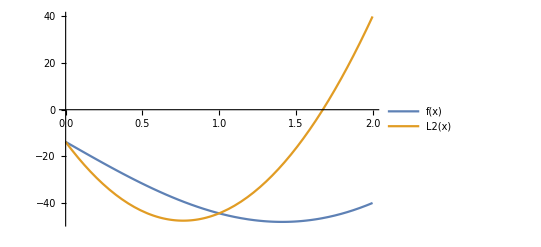

```mathematica
Plot[{f[x],L2[x]},{x,0,2},PlotLegends->"Expressions"] (*intervala ot tablicata*)
```

```mathematica
(*proverqvame usloviqta=>dali suvpadat stoinostite*)
```

```mathematica
L2[0]
```

-13.8

```mathematica
L2[1]
```

-44.4393

```mathematica
L2[2]
```

39.9896

```mathematica
(*namirame priblijenata stoinost na funkciqta v opredelenata tochka*)
```

```mathematica
f[s]
```

-31.7014

```mathematica
L2[s]
```

-43.5032

```mathematica
Print["istinskata greshka e ", Abs[L2[s]-f[s]]]
```

istinskata greshka e 11.8018